```mathematica
Clear["Global`*"]
```

```mathematica
Import[NotebookDirectory[]<>"QuaternionFunctions.m"]
```

# Beginning of stuff

```mathematica
R[theta_]:={{Cos[theta],-Sin[theta]},{Sin[theta],Cos[theta]}};
```

```mathematica
assumptions = {dtheta0∈Reals,ddtheta∈Reals,v1∈Reals,v0∈Reals,v1>0,v0>0,t1∈Reals,t2∈Reals, t1>=0,t2>=0,t>=0,t<=t2-t1};
```

```mathematica
ds=(v1-v0)/(t2-t1)*t+v0;
thetaWO=theta0+dtheta0 t+ddtheta t^2/2;
```

```mathematica
vW=R[thetaWO].{1,0}ds
aW=D[vW,t];
omega=D[thetaWO,t];
alpha=D[omega,t];
x=Assuming[assumptions, (Integrate[vW,{t,0,t}])+{x0,y0}];
```

{(v0+(t (-v0+v1))/(-t1+t2)) Cos[dtheta0 t+(ddtheta t^2)/2+theta0],(v0+(t (-v0+v1))/(-t1+t2)) Sin[dtheta0 t+(ddtheta t^2)/2+theta0]}

```mathematica
vApprox=Normal[Series[vW,{t,(t2-t1)/2,5}]];
xApprox=Assuming[assumptions,Integrate[Collect[vApprox,t,Simplify],{t,0,t}]]+{x0,y0};
xApprox=Simplify[xApprox,assumptions];
```

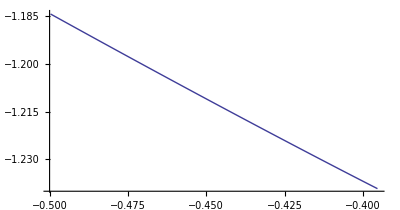

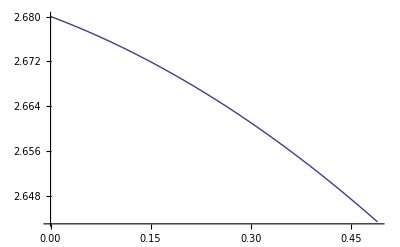

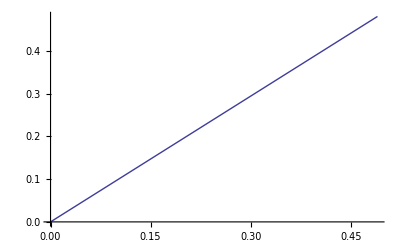

```mathematica
test={x0->-0.395366,y0->-1.239190,theta0->2.680030,dtheta0->-0.044754,ddtheta->-0.122891,v0->0.000000,v1->0.481007,t2->10.010000,t1->9.520000};
ParametricPlot[{xApprox/.test},{t,0,t2-t1/.test}]
Plot[thetaWO/.test,{t,0,t2-t1/.test}]
Plot[ds/.test,{t,0,t2-t1/.test}]
```

```mathematica
(*6DOF representation of odometric ref frame*)
Q={Cos[thetaWO/2],0,0,Sin[thetaWO/2]};
POSE=Flatten[{xApprox,0}];
VO=Flatten[{R[-thetaWO].vW,0}]//FullSimplify;
WO={0,0,omega};
AO=Flatten[{R[-thetaWO].aW,0}]//FullSimplify;
AlphaO={0,0,alpha};
```

```mathematica
(*put everything in sensor frame, certain rotations should have no effect*)
```

```mathematica
QOS={Sqrt[1-qOS1^2-qOS2^2-qOS3^2],qOS1,qOS2,qOS3};
SO={sO1,sO2,sO3};
```

```mathematica
POSEShatlong=POSE+QuatToRot[Q].SO;
(*POSEShat=ParallelTable[SimplifyQLite[POSEShatlong[[i]],{Q},{}],{i,1,3}];*)
```

```mathematica
QShat =QuatProd[Q,QOS];
```

```mathematica
VShatlong=QuatToRot[QuatInv[QOS]].(VO+Cross[WO,SO]);
(*VShat=ParallelTable[SimplifyQLite[VShatlong[[i]],{Q,QOS},{}],{i,1,3}];*)
```

```mathematica
WShat=QuatToRot[QuatInv[QOS]].WO;
```

```mathematica
AShat=QuatToRot[QuatInv[QOS]].(AO+Cross[WO,Cross[WO,SO]]+Cross[AlphaO,SO]);
```

```mathematica
AlphaShat=QuatToRot[QuatInv[QOS]].AlphaO;
```

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
(*separate blocks of the augmented state*)
MyStringWrite[ToGoodC[POSEShatlong],"YAMotionModel_POSE.mthout"];
MyStringWrite[ToGoodC[QShat],"YAMotionModel_Q.mthout"];
MyStringWrite[ToGoodC[VShatlong],"YAMotionModel_V.mthout"];
MyStringWrite[ToGoodC[WShat],"YAMotionModel_W.mthout"];
MyStringWrite[ToGoodC[AShat],"YAMotionModel_A.mthout"];
MyStringWrite[ToGoodC[AlphaShat],"YAMotionModel_Alpha.mthout"];

Run["python ../fixMathematicaOutput_v2.py YAMotionModel_POSE.mthout part 0 1"];
Run["python ../fixMathematicaOutput_v2.py YAMotionModel_Q.mthout part 0 1"];
Run["python ../fixMathematicaOutput_v2.py YAMotionModel_V.mthout part 0 1"];
Run["python ../fixMathematicaOutput_v2.py YAMotionModel_W.mthout part 0 1"];
Run["python ../fixMathematicaOutput_v2.py YAMotionModel_A.mthout part 0 1"];
Run["python ../fixMathematicaOutput_v2.py YAMotionModel_Alpha.mthout part 0 1"];
```

```mathematica
Run["python ../fixMathematicaOutput_v2.py YAMotionModel_POSE.mthout x 1 1"];
Run["python ../fixMathematicaOutput_v2.py YAMotionModel_Q.mthout q 1 1"];
Run["python ../fixMathematicaOutput_v2.py YAMotionModel_V.mthout v 1 1"];
Run["python ../fixMathematicaOutput_v2.py YAMotionModel_W.mthout w 1 1"];
Run["python ../fixMathematicaOutput_v2.py YAMotionModel_A.mthout a 1 1"];
Run["python ../fixMathematicaOutput_v2.py YAMotionModel_Alpha.mthout alpha 1 1"];
```